# Visualizing Chaos in the Physical Pendulum

In the laboratory we will investigate more of the behavior of the damped, non-linear, physical pendulum that was developed in the previous laboratory.

## 1. The Model.

The equation describing the physical pendulum can be written in terms of torques as

                                τ_total = Iα =  τ_gravity + τ_friction + τ_drive
                                                
where I is the moment of inertia, and α is the angular acceleration. The components of the total torque are summarized below.

                                              τ_gravity =    (-mg sinθ ) r_cm 
                                              
                                       τ_friction = -(br_cm dθ/dt) r_cm
                                       
                                       τ_drive = r_cm F_D sin(Ωt)

In the first expression in this list r_cm is the distance from the pivot to the center of mass, m is the mass, and  θ is the angle with respect to the vertical. In the second formula b is the drag coefficient detemined by the nature of the physical pendulum. The minus sign here is critical since this torque must oppose the motion. For the driving term, the last in the list,   F_D is the amplitude of the force and Ω is the angular frequency of the driving force.

The pendulum is a uniform cylinder that is pivoted at one end. The following inital conditions and parameters apply.

t_0 = 0.0 s                θ_0 = 1 rad               ω_0 = 0.0 rad/s

Length of pendulum:  30 m (it's big)
Drag coefficient: 1 kg/s
Mass of pendulum: 30 kg
Driving force amplitude: 100 N
Angular frequency of driving force: 0.66 rad/s

Integration step size: 0.01 s

## 2. Chaos.

We have now looked a phase-space for the simple pendulum and damped pendulum.  Under certain conditions deterministic systems can become chaotic.  The driven damped pendulum is a simple example of a chaotic system. (Use your algorithm improved from lab 7)

a. The most salient feature of dynamical chaos is sensitivity to initial conditions. This means that the same system with just slightly different initial conditions will follow a dramatically different trajectory. In fact, ‘adjacent’ sets of initial conditions give rise to exponentially diverging trajectories. Generating a phase-space plot for θ_0 = 1.1rad(63^o) and θ_0 = 1 rad. Compare these plots near t = 400s. 
(To only show the end of your list use listname[[35000;;40000]] to only view the last 5000 elements after the trasient period has ended. The 40000 assumes a maximum time 400 s and a step size of 0.01. 
For example: ListPlot[{positionvelocity1[[35000;;40000]],positionvelocity2[[35000;;40000]]}] )

 Does your model exhibit chaos? 

b. Change the driving force to 617 N and repeat part a.  Does your model exhitbit chaotic behavior?

## 3. The Poincare Section.

In the previous sections we found that the phase-space trajectory of the physical pendulum is complex and difficult to decipher. We now develop a technique to view what is called the Poincare section of the phase space of the sytem.

Consider a phase-space trajectory of a dynamical system like the one we generated for the realistic physical pendulum. The system clearly fell within some well-defined limits in terms of θ and ω, but within those limits the trajectory was very complicated. The Poincare section is a 'stroboscopic' view of the phase-space trajectory that enables us to see the region of phase space the system occupies.

An essential component of the onset of chaos is the presence of the driving force. We will use the periodicity of the driving term to investigate the phase space of our physical pendulum in the following way. (1) A phase-space trajectory is developed with the same algorithms we've used before. (2) Instead of plotting every point we only plot those times that are in phase with the driving torque.  (Or have the same period as the driving force) In other words, we only plot those points on our phase-space trajectory where t = n2π/ω_drive where n is an integer.

## 3. Sample Code.

To generate the Poincare section for the physical pendulum we need to incorporate a few new components into our code.  Highlighted below are the new components.  omega2 is the angular frequency of the solution.  For an nondamped nondriven pendulum it is the natural frequency √(rmg/Inertia).  For a driven pendulum it is the drive frequency.

              dx^2/dt^2 = -x           x(t=0) = 1.0               x'(t=0) = 0.2
              
We will keep only those points when t=nπ.

```mathematica
(* initial conditions and parameters *)
t0 = 0.0;
x0 = 1.0;
v0 = 0.2;
step = 0.01;
omega2 = 1;
(* get the second and third points
	  on the curve *)

t1 = t0 + step;
x1 = x0 + step*v0;
x2 = 2*x1 - x0 - (step*step*x1);
v1 = (x2 - x0)/(2*step);

(* put the first point in the table *)

MyTable = {{x0,v0},{x1,v1}};

(* Now use a Do loop and store the points
		 when t = nπ. a centered formula is used
	  to approximate the second derivative. 

   parameters needed to test when to store
		 the data. *)

TimeTest0 =2*Pi/omega2 ;
TimeTest=TimeTest0;
PeriodCounter = 1;

(* first point of the algorithm *)

xminus = x0;
xmid = x1;
xplus = x2;
tmin = t1 + step;
tmax = 50.0;

Do[xminus = xmid;
	     xmid = xplus;
	     xplus = 2*xmid - xminus - (step*step*xmid);
	     vmid = (xplus - xminus)/(2*step);
		  If[t> TimeTest,
		         MyTable = Append[MyTable,{xmid,vmid}];
		         PeriodCounter = PeriodCounter + 1;
		         TimeTest = PeriodCounter*TimeTest0
		       ],
	     {t,tmin,tmax,step}
  ]
```

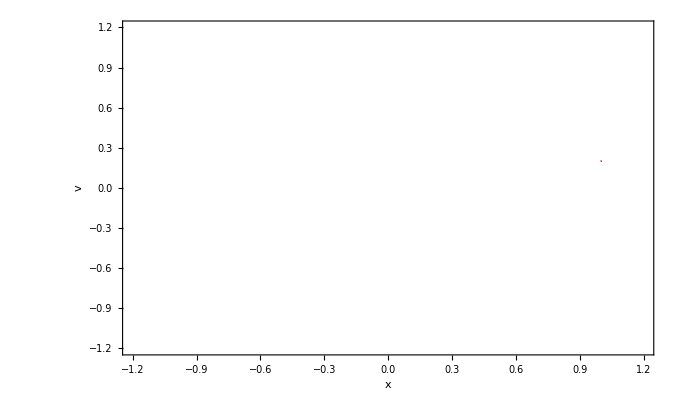

```mathematica
ListPlot[MyTable,PlotRange->{{-1.2,1.2},{-1.2,1.2}},Joined->False,Frame->True,FrameLabel->{"x","v","",""},PlotStyle->{RGBColor[1,0,0],PointSize[0.0002]}]
```

## 4. Investigating the Physics.

Generate a Poincare section for the physical pendulum.  Use small angle conditions to look at your system (make sure you set θ_0 = 0.1 rad   and   ω_0 = 0.0 rad/s). Once you have a working code consider the following questions.

a. What does the Poincare section look like when you turn off the torques due to friction and the driving term? (remember in this case  t = n*2*pi/w  where omega2 =√(rmg/Inertia) is for the pendulum with graity only) The language used to describe the features you discover here is that the system is drawn to the surface defined by the Poincare section. This surface is called an attractor. What would you name the attractor for this system?  [you may want to use PlotRange→{{-.5,.5},{-.5,.5}}]

b. What does the Poincare section look like when you turn on the torque due to friction, but keep the driving term turned off? 
(t = n*2*pi/w  where omega2 = √(rmg/Inertia-(bL^2/(2Inertia))^2) for a damped physical pendulum using small angle approximation.  What would you name the attractor for this system with the damping term turned on?

c. Turn everything on and generate the Poincare section. (Fd = 100 and now omega2 = Ωdrive) What does it look like? Compare this result with parts 4.a and 4.b. The surface you have discovered is called a strange attractor .  [you may need to change your PlotRange→{{-Pi,Pi},{-3,3}}]

d. What happens to the strange attractor if you change the driving force to 700?  What happens to the strange attractor if you change the drag coefficient? What happens if you change in initial angle?

e. Numerical methods  enable us to examine systems that are much more complex than before now. In the course of studying systems like the non-linear, damped, forced, physical pendulum that you have just studied we observe an extreme sensitivity to the initial conditions. What impact, if any, does this sensitivity have on the predictive power of our models of complex systems?

(turn in section 4 to chelms netfiles)